```mathematica
NDSolve[{u'[t]==u[t](1-v[t]),v'[t]==0.5 v[t](u[t]-1),u[0]==1,v[0]==3},{u,v},{t,0,40}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

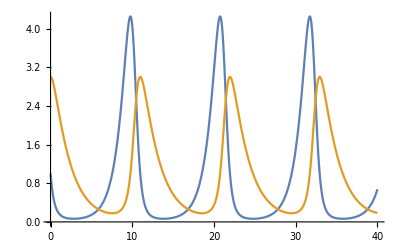

```mathematica
Plot[{Evaluate[u[t]/.%2],Evaluate[v[t]/.%2]},{t,0,40}]
```

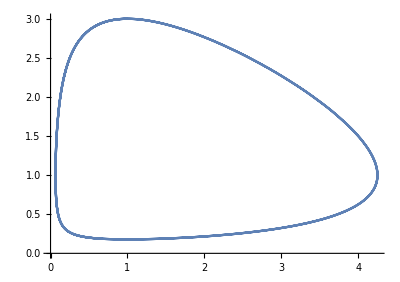

```mathematica
ParametricPlot[{Evaluate[{u[t], v[t]}/.%2]}, {t,0,40}]
```